# Orbigraphs: Defining a Graph Theoretic Analog to Riemannian Orbifolds

## Sam Stewart and Colin Gavin Lewis & Clark College - Portland, OR | -Graphics-

```mathematica
AppendTo[$Path,NotebookDirectory[]];
<<"Orbigraphs.m"
```

## Outline

Manifolds to Regular Graphs

Orbifolds to Orbigraphs

Orbigraph Structure

Spectral Geometry of Orbigraphs

## Manifolds

Manifolds: topological spaces that are locally modeled on ℝ^n

Surfaces in ℝ^3 locally look like ℝ^2

Example: S^2

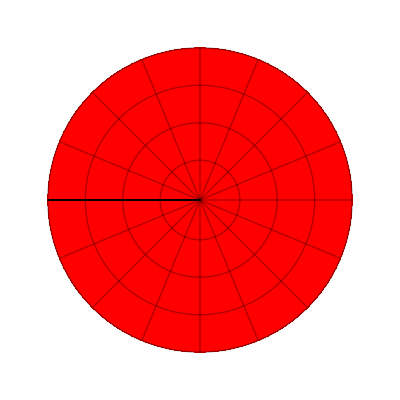
| ⟶ | -Graphics-

```mathematica
s=RevolutionPlot3D[{Sqrt[1-t^2],t},{t,-1,0.5},{θ,0,2π},PlotStyle->Blue,PlotRange->{{-1,1},{-1,1},{-1,1}},Mesh->{9,15}];
c=RevolutionPlot3D[{Sqrt[1-t^2],t},{t,0.5,1},{θ,0,2π},PlotStyle->Red,Mesh->{3,15}];
sphereFrames=Table[Rasterize@Show[s,c,SphericalRegion->True,ViewVector->{4 Sin[t],4 Cos[t],2},ImageSize->{200,200},Axes->False,Boxed->False],{t,0,2π,2π/100}];
maniChart=RegionPlot[x^2+y^2≤Sqrt[1-0.5^2],{x,-1,1},{y,-1,1},PlotStyle->Red,Mesh->{3,15},Frame->False,Axes->False,MeshFunctions->{Norm[{#1,#2}]&,ArcTan[#1,#2]&},PlotPoints->100];
{{Dynamic[sphereFrames⟦Clock[{1,101,1},10]⟧],"⟶",maniChart}}//Grid
```

## Manifolds to Regular Graphs

k-regular graphs: undirected graphs with constant degree k

```mathematica
Grid[List@Take[SetProperty[#,{ImageSize->110,VertexSize->0.2}]&/@ImportRegularGraphs[8,4],3],Frame->All]
```

-Graphics- | -Graphics- | -Graphics-

Neighborhoods of vertices look like k-stars:

```mathematica
hi={Style[1,Red],Style[{2,1<->2,3,1<->3,4,1<->4,5,1<->5},Thick,Blue]};
Row[{
HighlightGraph[SetProperty[ImportRegularGraphs[8,4]⟦3⟧,{VertexSize->0.2,EdgeStyle->Thick,ImageSize->150}],hi],
"⟶",
SetProperty[HighlightGraph[StarGraph[5,VertexSize->0.2],hi],ImageSize->150]}]
```

-Graphics-⟶-Graphics-

## Orbifolds

Orbifolds: manifolds with some singular points

Appear as a tool in geometry and an object of study on their own

Example: S^2 with a cone point

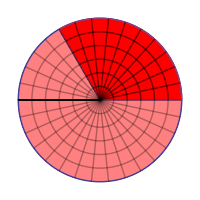
| ⟶ | -Graphics-
ℤ_3 ⟳ D^2

```mathematica
teardrop=Piecewise[{{1/Sqrt[3]*x,x≤Sqrt[3]},{Sqrt[4/3-(x-4/Sqrt[3])^2],Sqrt[3]<x≤2*Sqrt[3]}}];
cone=RevolutionPlot3D[{teardrop,-x},{x,0,1},{θ,0,2π},Mesh->{5,10},PlotRange->{{-2,2},{-2,2},{-4,0}},PlotStyle->Red];
bulb=RevolutionPlot3D[{teardrop,-x},{x,1,2Sqrt[3]},{θ,0,2π},Mesh->{10,10},PlotRange->{{-2,2},{-2,2},{-4,0}},Exclusions->None,PlotStyle->Blue];
orbiFrames=Table[Rasterize@Show[cone,bulb,SphericalRegion->True,Axes->False,ViewVector->{7 Sin[t],7 Cos[t],2},Boxed->False,ImageSize->{200,200}],{t,0,2π,2π/100}];
orbiChart=Column[{RegionPlot[{x^2+y^2≤1,x^2+y^2≤1&&0≤ArcTan[x,y]≤2π/3},{x,-1,1},{y,-1,1},PlotStyle->{Pink,Red},Frame->False,Axes->False,Mesh->{5,Table[ø,{ø,-π,π,2π/30}]},ImageSize->{200,200},MeshFunctions->{Norm[{#1,#2}]&,ArcTan[#1,#2]&},PlotPoints->100],"ℤ_3 ⟳ D^2"},Center];
{{Dynamic[orbiFrames⟦Clock[{1,101,1},10]⟧],"⟶",orbiChart}}//Grid
```

## Orbifolds to Orbigraphs

Want to complete the analogy: “__________ are to regular graphs as orbifolds are to manifolds”

Neighborhoods: look like quotients of directed k-stars

```mathematica
multiArrows[adj_,pts_List,e_]:=Module[{bumps,es,normal},
es=adj⟦e⟦1⟧,e⟦2⟧⟧;
If[es<2,Return[Arrow[pts]]];
normal=Cross[pts⟦2⟧-pts⟦1⟧];
bumps=Table[normal*(n 0.6/(es-1)-0.3),{n,0,es-1}];
Arrow[BezierCurve[{pts⟦1⟧,Mean@pts+#,pts⟦2⟧}]]&/@bumps];

s=StarGraph[7,DirectedEdges->True,VertexStyle->{1->Blue,2->Green,3->Yellow,4->Purple,5->Orange,6->Red,7->Red},EdgeStyle->{1->6->{Thick,Red},1->7->{Thick,Red},1->2->Green,1->3->Yellow,1->4->Purple,1->5->Orange},VertexSize->0.1,ImageSize->100];

orbiStar=OrbigraphFromGroup[s,PermutationGroup[{Cycles[{{2,3}}]}]];

orbiStar=SetProperty[orbiStar,{GraphLayout->"RadialEmbedding",VertexSize->0.1,ImageSize->{200,200},EdgeLabels->None,EdgeShapeFunction->(multiArrows[WeightedAdjacencyMatrix@orbiStar,#1,#2]&)}];
orbiStar=SetProperty[orbiStar,
{VertexStyle->{1->Blue,2->Red,3->Green,4->Yellow,5->Purple,6->Orange},
EdgeStyle->{1->6->Orange,1->2->{Thick,Red},1->3->Green,1->4->Yellow,1->5->Purple},
ImageSize->100}];
{{"ℤ_2⟳",s,
"⟶",
orbiStar}}//Grid
```

ℤ_2⟳ | -Graphics- | ⟶ | -Graphics-

Compatibility condition: if there is an edge from v_1 to v_2 then there is one from v_2 to v_1

```mathematica
SetProperty[AdjacencyOrbigraph@{{0,2},{1,0}},VertexLabels->{1->Subscript[v, 2],2->Subscript[v, 1]}]
```

-Graphics-

## Building an Orbigraph

Start with quotients of directed k-stars

Merge according to compatibility condition

```mathematica
mergingEdgeShape[s_,t_]:={pts,e}↦Arrow[BezierCurve[{pts⟦1⟧,Mean[pts]+Cross[pts⟦2⟧-pts⟦1⟧]*0.4(0.2t+s),pts⟦2⟧}]];
mergingGraph[t_]:=Graph[{1->1,1->2,1->5,3->4,3->6,3->7},
VertexCoordinates->{1->{0.5t,0},2->{1+0.5t,0},3->{3-0.5t,0},4->{2-0.5t,0},5->{1+0.5t,0},6->{2-0.5t,0},7->{2-0.5t,0}},
VertexSize->{1->{0.04,0.04},3->{0.04,0.04},2->0,4->0,5->0,6->0,7->0},
PlotRange->{{-0.5,3.5},{-1,1}},
EdgeStyle->{1->2->Red,1->5->Red,1->1->Blue,3->4->Orange,3->6->Orange,3->7->Orange},
EdgeShapeFunction->{
1->2->mergingEdgeShape[t,-2],
3->4->mergingEdgeShape[t,0],
1->5->mergingEdgeShape[t,2],
3->6->mergingEdgeShape[t,-2],
3->7->mergingEdgeShape[t,2]},
ImageSize->{400,200},
EdgeStyle->Thick,
PerformanceGoal->"Quality"];
Animate[mergingGraph[t],{t,0,2},DefaultDuration->2,AnimationRepetitions->1,AnimationRunning->False]
```

## Spectral Geometry

Idea: Investigating the resonant frequencies of an object tells us about the geometry

```mathematica
ClearAll[r];
drumSolution[k_,l_,tf_,af_,r0_]:=Module[{μ=BesselJZero[k,l]/r0},tf[μ t0]af[k θ]BesselJ[k,μ r]//N];
drumPlot[t_,r0_]:=ParametricPlot3D[Evaluate@{r Cos[θ],r Sin[θ],drumSolution[1,1,Cos,Cos,r0]/.t0->t},
{r,0,r0},{θ,0,2π},
PlotRange->{-2,2},
ImageSize->300,
ViewPoint->{2.42,-1.61,1.72},
Axes->None,
Boxed->False];
period=4π/BesselJZero[1,1];
drumFrames=Table[Rasterize@Grid[{{drumPlot[t,1],drumPlot[t,2]},{"r=1","r=2"}}],
{t,0,period,0.05}];
Dynamic[n=Clock[{1,Length[drumFrames],1},2];drumFrames⟦n⟧]
```

## Spectral Graph Theory

For graphs, consider the eigenvalues of the adjacency matrix

```mathematica
exGr=CompleteGraph[4,ImageSize->200];
Row[{exGr," ⟶ ",AdjacencyMatrix@exGr//MatrixForm," ⟶ ",Eigenvalues@AdjacencyMatrix@exGr}]
```

-Graphics- ⟶ (0 | 1 | 1 | 1
1 | 0 | 1 | 1
1 | 1 | 0 | 1
1 | 1 | 1 | 0) ⟶ {3,-1,-1,-1}

Many results about k-regular graphs hold for k-orbigraphs

Spectral radius is k

Bipartite if and only if spectrum is symmetric about zero

## Spectral Bounds on Singular Points

Theorem: If Γ is a k-orbigraph on n vertices with spectrum λ_1,…,λ_n and s singular points, then we have:

(∑_i λ_i^2-n k)/(k^2-k)≤s≤∑_i (λ_i^2-n k)

Example:

```mathematica
singularEx=SetProperty[AdjacencyOrbigraph@({{0, 0, 1, 2}, {0, 0, 2, 1}, {1, 1, 1, 0}, {1, 1, 0, 1}}),ImageSize->200];
spec=OrbigraphSpectrum@singularEx;
Row@{singularEx," ⟶ ",Sort[spec,Less]," ⟶ ",(Total[spec^2]-12)/6≤"s"≤Total[spec^2]-12}
```

-Graphics- ⟶ {-2,0,1,3} ⟶ 1/3≤s≤2